```mathematica
SetOptions[Plot,BaseStyle->{FontFamily->"Helvetica",FontSize->24},Frame->True,FrameStyle->Black];SetOptions[ListPlot,BaseStyle->{FontFamily->"Helvetica",FontSize->24},Frame->True,FrameStyle->Black];yrotmatelem[k_,kp_,θ_,ϕ_]:=Exp[-I*(2*k-Np)*ϕ/2]*Sqrt[((k!)*((Np-k)!)*(kp!)*((Np-kp)!))]*Sum[(((-1.0)^n)*(Cos[θ/2]^(k-kp+Np-2*n))*(Sin[θ/2]^(2*n+kp-k)))/(((k-n)!)*((Np-kp-n)!)*(n!)*((kp-k+n)!)),{n,Max[k-kp,0],Min[k,Np-kp]}];
psi[k1_,k2_,k3_,k4_]=(1/4^Np)*Sqrt[Binomial[Np,k1]*Binomial[Np,k2]*Binomial[Np,k3]*Binomial[Np,k4]];
```

```mathematica
Np=2;
dim=(Np+1)^4;θ=Pi/2;ϕ=0;clusterstate=ArrayReshape[Table[KroneckerDelta[k1,k2]*KroneckerDelta[k3,k4]*Sum[((-1)^(Np-k1-k3+l))*Binomial[k1,l]*Binomial[Np-k1,k3-l]/Binomial[Np,k3],{l,0,Min[k1,k3]}],{k1,0,Np},{k2,0,Np},{k3,0,Np},{k4,0,Np}],{1,(Np+1)^4}][[1]];
clusterstate=N[Normalize[clusterstate]];
projmatz=ArrayReshape[Table[KroneckerDelta[k1,k1p]*KroneckerDelta[k2,k2p]*KroneckerDelta[k3,k3p]*KroneckerDelta[k4,k4p]*KroneckerDelta[k1,k2]*KroneckerDelta[k3,k4],{k1,0,Np},{k2,0,Np},{k3,0,Np},{k4,0,Np},{k1p,0,Np},{k2p,0,Np},{k3p,0,Np},{k4p,0,Np}],{(Np+1)^4,(Np+1)^4}];
psivec0=ArrayReshape[Table[psi[k1,k2,k3,k4],{k1,0,Np},{k2,0,Np},{k3,0,Np},{k4,0,Np}],{1,(Np+1)^4}][[1]];
Urot12=ArrayReshape[Table[yrotmatelem[k1p,k1,θ,ϕ]*yrotmatelem[k2p,k2,θ,ϕ]*KroneckerDelta[k3,k3p]*KroneckerDelta[k4,k4p],{k1,0,Np},{k2,0,Np},{k3,0,Np},{k4,0,Np},{k1p,0,Np},{k2p,0,Np},{k3p,0,Np},{k4p,0,Np}],{(Np+1)^4,(Np+1)^4}];
Urot34=ArrayReshape[Table[yrotmatelem[k3p,k3,θ,ϕ]*yrotmatelem[k4p,k4,θ,ϕ]*KroneckerDelta[k2,k2p]*KroneckerDelta[k1,k1p],{k1,0,Np},{k2,0,Np},{k3,0,Np},{k4,0,Np},{k1p,0,Np},{k2p,0,Np},{k3p,0,Np},{k4p,0,Np}],{(Np+1)^4,(Np+1)^4}];
```

```mathematica
targetlist123={};
targetlist234={};
targetlist123b={};
For[k1=0,k1≤Np,k1=k1+1,
For[k2=0,k2≤Np,k2=k2+1,
For[k3=0,k3≤Np,k3=k3+1,
For[k4=0,k4≤Np,k4=k4+1,
If[(k1+k2+k3-Np≥0),
targetlist123=Append[targetlist123,{k1,k2,k3,k4}];
];
If[(-k1+k2-k3+Np>=0),
targetlist123b=Append[targetlist123b,{k1,k2,k3,k4}];
];
If[(k2+k3+k4-Np≥0),
targetlist234=Append[targetlist234,{k1,k2,k3,k4}];
];
];
];
];
];
projmatx1230=ArrayReshape[Table[KroneckerDelta[k1,k1p]*KroneckerDelta[k2,k2p]*KroneckerDelta[k3,k3p]*KroneckerDelta[k4,k4p]*If[MemberQ[targetlist123,{k1,k2,k3,k4}],1,0],{k1,0,Np},{k2,0,Np},{k3,0,Np},{k4,0,Np},{k1p,0,Np},{k2p,0,Np},{k3p,0,Np},{k4p,0,Np}],{(Np+1)^4,(Np+1)^4}];
projmatx123b0=ArrayReshape[Table[KroneckerDelta[k1,k1p]*KroneckerDelta[k2,k2p]*KroneckerDelta[k3,k3p]*KroneckerDelta[k4,k4p]*If[MemberQ[targetlist123b,{k1,k2,k3,k4}],1,0],{k1,0,Np},{k2,0,Np},{k3,0,Np},{k4,0,Np},{k1p,0,Np},{k2p,0,Np},{k3p,0,Np},{k4p,0,Np}],{(Np+1)^4,(Np+1)^4}];
projmatx2340=ArrayReshape[Table[KroneckerDelta[k1,k1p]*KroneckerDelta[k2,k2p]*KroneckerDelta[k3,k3p]*KroneckerDelta[k4,k4p]*If[MemberQ[targetlist234,{k1,k2,k3,k4}],1,0],{k1,0,Np},{k2,0,Np},{k3,0,Np},{k4,0,Np},{k1p,0,Np},{k2p,0,Np},{k3p,0,Np},{k4p,0,Np}],{(Np+1)^4,(Np+1)^4}];
projmatx123=ConjugateTranspose[Urot12].projmatx1230.Urot12;
projmatx123b=ConjugateTranspose[Urot12].projmatx123b0.Urot12;
projmatx234=ConjugateTranspose[Urot34].projmatx2340.Urot34;
```

```mathematica
sol=Eigensystem[projmatz.projmatx234.projmatx123.projmatx123b];
sol[[1]]
```

{1.,0.903851,0.850352,0.66144,0.589087,0.582545,0.415934,0.337836,0.291767,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
sol[[2]][[1]]
sol[[2]][[2]]
```

{-0.353553,0.,0.,0.,0.353553,0.,0.,0.,-0.353553,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.353553,0.,0.,0.,-2.34065×10^-16,0.,0.,0.,-0.353553,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.353553,0.,0.,0.,-0.353553,0.,0.,0.,-0.353553}

{-0.0833044,0.,0.,0.,-0.199225,0.,0.,0.,-0.0833044,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.238114,0.,0.,0.,-8.53704×10^-17,0.,0.,0.,-0.238114,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.209769,0.,0.,0.,0.86315,0.,0.,0.,-0.209769}

```mathematica
clusterstate.projmatz.projmatx234.projmatx123.projmatx123b.clusterstate
```

1.

```mathematica
clusterstate
```

{0.353553,0.,0.,0.,-0.353553,0.,0.,0.,0.353553,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.353553,0.,0.,0.,0.,0.,0.,0.,0.353553,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.353553,0.,0.,0.,0.353553,0.,0.,0.,0.353553}

```mathematica
Chop[Urot12.clusterstate]
```

{0,0,0,0,0,0,0,0,0.353553,0,0,0,0,-0.25,0,0,0,0,0.353553,0,0,0,0,0,0,0,0,0,0,0,0,-0.25,0,0,0,0,0.353553,0,0,0,0,0,0,0,0.353553,0,0,0,0,-0.25,0,0,0,0,0.353553,0,0,0,0,0,0,0,0,0,0,0,0,-0.25,0,0,0,0,0,0,0,0,0,0,0,0,0.353553}

```mathematica
projmatx1230//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Urot34.clusterstate
```

{0.,-0.5,-0.5,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.5,0.,0.,0.5}

```mathematica
projmatx2340//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
noiter=100;
psiiter=Normalize[MatrixPower[projmatz.projmatx234.projmatx123.projmatx123b,noiter].psivec0]
clusterstate.psiiter
```

{0.353552,0.,0.,0.,-0.353556,0.,0.,0.,0.353552,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.35355,0.,0.,0.,-2.21615×10^-8,0.,0.,0.,0.35355,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.353551,0.,0.,0.,0.353564,0.,0.,0.,0.353551}

1.

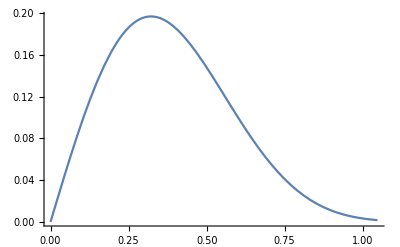

```mathematica
nd=1;nc=10-nd;
Plot[{(Cos[x]^nc)*(Sin[x]^nd)},{x,0,Pi/(Sqrt[nc])},PlotRange->All]
```

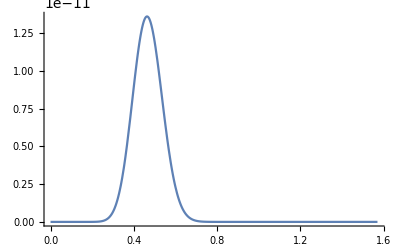

```mathematica
nd=20;nc=100-nd;
Plot[{(Cos[x]^nc)*(Sin[x]^nd)},{x,0,Pi/2},PlotRange->All]
```